# Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Miguel\Github\quantum_chaotic_channels\MG files\Random Kraus on a qubit

```mathematica
Get["C:\\Users\\Miguel\\Github\\quantum_chaotic_channels\\Mathematica_packages\\QMB.wl"]
Get["C:\\Users\\Miguel\\Github\\quantum_chaotic_channels\\Mathematica_packages\\Chaometer.wl"]
```

```mathematica
KroneckerVectorProduct[a_,b_]:=Flatten[KroneckerProduct[a,b]];
BlochVector[ρ_]:=Tr[Pauli[#].ρ]&/@Range[3];
Parity[ψ_,L_]:=ψ[[FromDigits[Reverse[#],2]+1&/@Tuples[{0,1},L]]];
Braket[a_,b_]:=Conjugate[a].b;
MeanLevelSpacingRatio[eigenvalues_]:=Mean[Min/@Transpose[{#,1/#}]&[Ratios[Differences[eigenvalues]]]];
Clear[SurvivalProbability];
SurvivalProbability[ψt_,ψ0_]:=Abs[Braket[ψ0,ψt]]^2;
```

```mathematica
Clear[bloch];
bloch[rho_]:={2Re[rho[[1,2]]],-2Im[rho[[1,2]]],rho[[1,1]]-rho[[2,2]]};
(*Plot Bloch sphere with Bloch vector*)
plotsphere=SphericalPlot3D[1,{theta,0,Pi},{phi,0,2 Pi},PlotStyle->Opacity[0.07],PlotRange->{{-1,1},{-1,1},{-1,1}},Boxed->False,Axes->False];
plotsphere2=Graphics3D[{Opacity[0.3],Sphere[{0,0,0},1]}];
Clear[rho];
rho[vec_]:={{vec[[1]],vec[[2]]},{vec[[3]],vec[[4]]}};
Clear[haar];
haar[dim_Integer]:=Module[{l=2^dim,state1},
state1=Table[RandomReal[NormalDistribution[],2],{l}];
Normalize[state1[[All,1]]+I state1[[All,2]]]
];
(*Define the Pauli matrices*)
sx={{0,1},{1,0}};
sy={{0,-I},{I,0}};
sz={{1,0},{0,-1}};
(*Define collective spin operators for n spins*)
Clear[Jx,Jy,Jz];
Jx[n_]:=(1/2)Sum[KroneckerProduct@@Table[If[j==i,sx,IdentityMatrix[2]],{j,n}],{i,n}];
Jy[n_]:=(1/2)Sum[KroneckerProduct@@Table[If[j==i,sy,IdentityMatrix[2]],{j,n}],{i,n}];
Jz[n_]:=(1/2)Sum[KroneckerProduct@@Table[If[j==i,sz,IdentityMatrix[2]],{j,n}],{i,n}];
(*Define the Lipkin Hamiltonian*)
Clear[Hlmg];
Hlmg[α_,gx_,gy_,n_]:=α*Jz[n]+(gx/(n-1))(Jx[n].Jx[n])+(gy/(n-1))(Jy[n].Jy[n]);
```

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

### Ensemble of initial states ψ_s ⊗ ψ_e, Chaotic

# Purities

```mathematica
L=6;
hx=1;
J=2;
hz=0.5;
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
(*L=5;
Δ=1.;
H=ClosedXXZHamiltonian[L,Δ];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];*)
ale2=30;
coloursc=Table[RGBColor[i,i/ale2,1-i],{i,ale2}];
blochtest=Table[qubit[i,0],{i,0,Pi,Pi/(ale2-1)}];
```

```mathematica
ψTa=qubit[0,0];
ψa=Table[Flatten[KroneckerProduct[ψTa,coherentstate[i,L-1]]],{i,blochtest}];
eigenψa=ParallelTable[Conjugate[eigenvec].i,{i,ψa}];
iprsa=ParallelTable[Total[Abs[i]^4],{i,eigenψa}];
energiesa=Table[Chop[Conjugate[i].H.i],{i,ψa}];
```

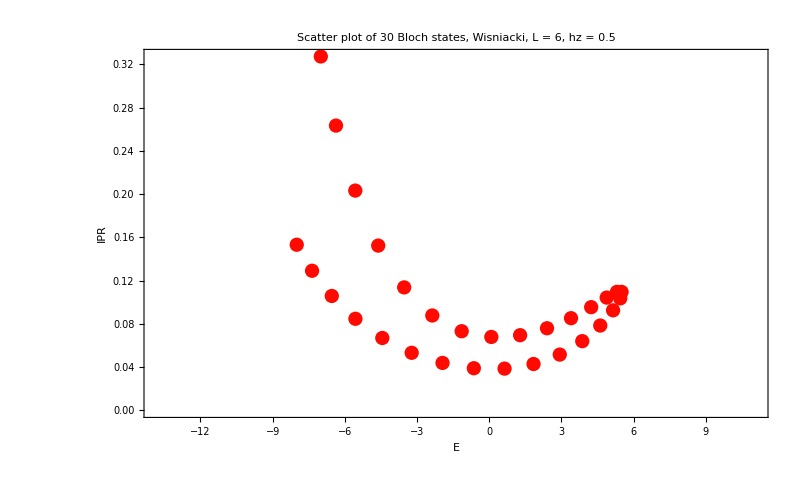

```mathematica
ListPlot[Transpose[{energiesa,iprsa}],PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale2]<>" Bloch states, Wisniacki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->coloursc[[1]],PlotRange->{{Min[eigenval],Max[eigenval]},All},ImageSize->800,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],HoldForm[TraditionalForm[IPR]]}]
```

```mathematica
tf=10.;
dt=0.1;
tlist=Range[0,tf,dt];
ψat=Table[StateEvolution[t,j,eigenval,eigenvec],{j,ψa},{t,0,tf,dt}];
```

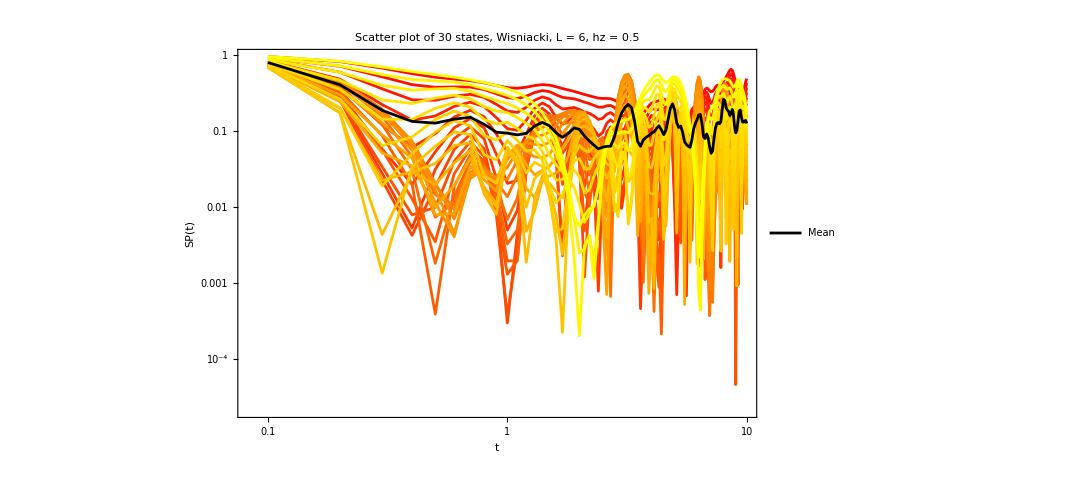

```mathematica
singlea=ListLogLogPlot[Table[{tlist[[i]],Abs[Conjugate[ψat[[j,1]]].ψat[[j,i]]]^2},{j,Length[ψat]},{i,Length[Range[0,tf,dt]]}],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale2]<>" states, Wisniacki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->coloursc,PlotRange->All,ImageSize->700,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["SP(t)"]}];
meana=ListLogLogPlot[Mean[Table[{tlist[[i]],Abs[Conjugate[ψat[[j,1]]].ψat[[j,i]]]^2},{j,Length[ψat]},{i,Length[Range[0,tf,dt]]}]],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale2]<>" states, Wisniacki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Directive[Black,Opacity[1]]},PlotRange->All,ImageSize->700,PlotLegends->{Style["Mean",Black]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["SP(t)"]}];
sp=Show[{singlea,meana},ImageSize->800]
```

```mathematica
ψat=Table[StateEvolution[t,j,eigenval,eigenvec],{j,ψa},{t,0,tf,dt}];
data={};
data2={};
Do[
densitya=Table[Dyad[j,j],{j,ψat[[k,All]]}];
reduceda=Table[Chop[MatrixPartialTrace[i,2,{2,2^(L-1)}]],{i,densitya}];
AppendTo[data2,reduceda];
puritiesa=Table[Chop[Purity[i]],{i,reduceda}];
AppendTo[data,puritiesa];
,{k,ale2}];
```

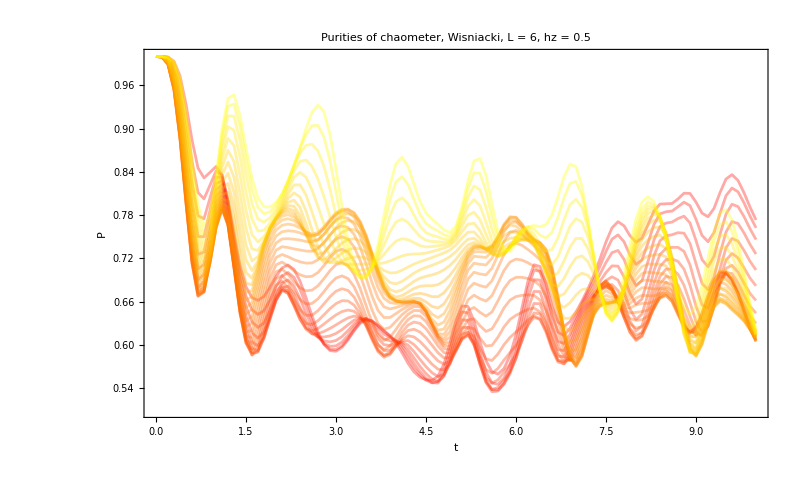

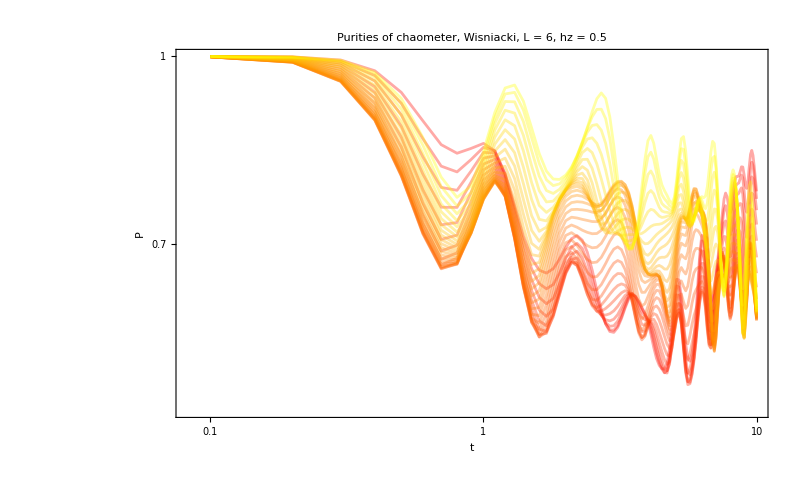

```mathematica
tlist=Range[0,tf,dt];
uno=ListPlot[Table[Transpose[{tlist,i}],{i,data}],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Purities of chaometer, Wisniacki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->Table[Directive[j,Opacity[0.35]],{j,coloursc}],PlotRange->All,ImageSize->800,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],HoldForm[P]}]
logpurity=ListLogLogPlot[Table[Transpose[{tlist,i}],{i,data}],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Purities of chaometer, Wisniacki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->Table[Directive[j,Opacity[0.35]],{j,coloursc}],PlotRange->All,ImageSize->800,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],HoldForm[P]}]
```

```mathematica
data2x={};
data2y={};
data2z={};
Do[
reducedmagax=Table[Chop[Tr[sx.i]],{i,data2[[k,All]]}];
reducedmagay=Table[Chop[Tr[sy.i]],{i,data2[[k,All]]}];
reducedmagaz=Table[Chop[Tr[sz.i]],{i,data2[[k,All]]}];
AppendTo[data2x,reducedmagax];
AppendTo[data2y,reducedmagay];
AppendTo[data2z,reducedmagaz];
,{k,ale2}];
```

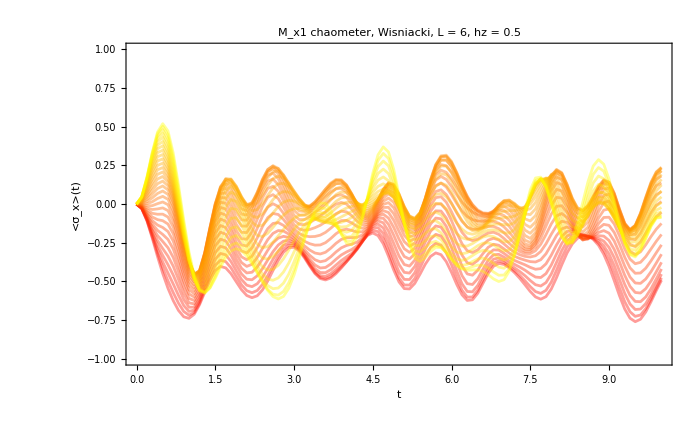

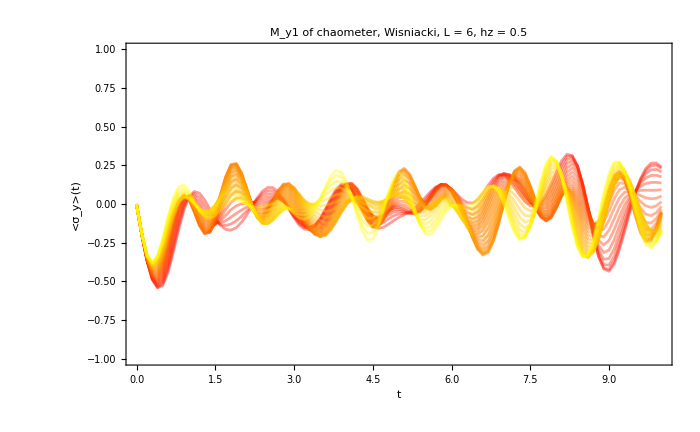

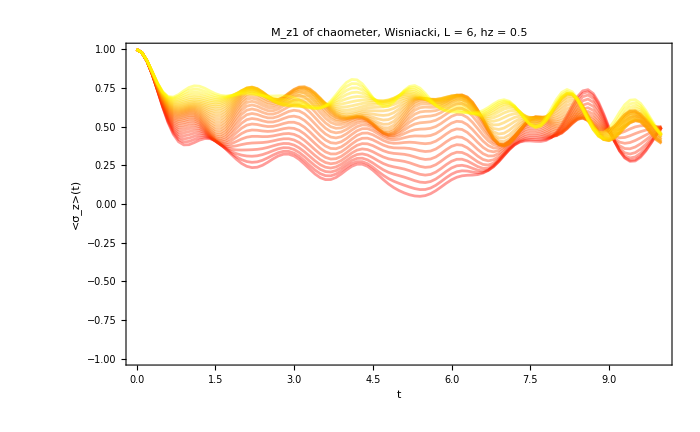

```mathematica
ListPlot[Table[Transpose[{tlist,k}],{k,data2x}],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["M_x1 chaometer, Wisniacki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->Table[Directive[j,Opacity[0.4]],{j,coloursc}],PlotRange->{All,{-1,1}},ImageSize->700,PlotLegends->Style["M_x(t)",Black,25],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["<σ_x>(t)"]}]
ListPlot[Table[Transpose[{tlist,k}],{k,data2y}],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["M_y1 of chaometer, Wisniacki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->Table[Directive[j,Opacity[0.4]],{j,coloursc}],PlotRange->{All,{-1,1}},ImageSize->700,PlotLegends->Style["M_y(t)",Black,25],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["<σ_y>(t)"]}]
ListPlot[Table[Transpose[{tlist,k}],{k,data2z}],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["M_z1 of chaometer, Wisniacki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->Table[Directive[j,Opacity[0.4]],{j,coloursc}],PlotRange->{All,{-1,1}},ImageSize->700,PlotLegends->Style["M_z(t)",Black,25],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["<σ_z>(t)"]}]
```

## Environment purities

```mathematica
ψat=Table[StateEvolution[t,j,eigenval,eigenvec],{j,ψa},{t,0,tf,dt}];
```

```mathematica
data={};
Do[
densitya=Table[Dyad[j,j],{j,ψat[[k,All]]}];
reduceda=Table[Chop[MatrixPartialTrace[i,1,{2,2^(L-1)}]],{i,densitya}];
puritiesa=Table[Chop[Purity[i]],{i,reduceda}];
AppendTo[data,puritiesa];
,{k,ale2}];
```

```mathematica
tlist=Range[0,tf,dt];
```

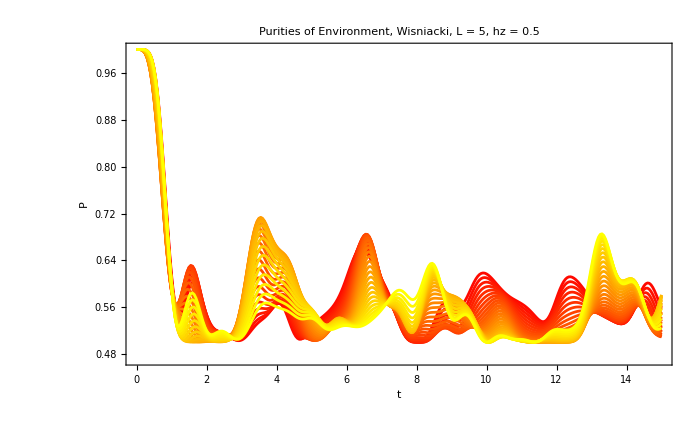

```mathematica
dos=ListPlot[Table[Transpose[{tlist,i}],{i,data}],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Purities of Environment, Wisniacki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->coloursc,PlotRange->All,ImageSize->700,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],HoldForm[P]}]
```

# Product states characterization

```mathematica
L=5;
hx=1;
J=1;
hz=0.5;
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
ipreigen=ParallelTable[Total[Abs[i]^4],{i,eigenvec}];
```

```mathematica
ale=500;
caometer=Table[haar[1],{i,ale}];
ale2=30;
coloursc=Table[RGBColor[i,i/ale2,1-i],{i,ale2}];
(*coloursc=Table[RGBColor[1-i,i/ale2,1-i],{i,ale2}];*)
single=qubit[0,0];
(*blochtest=Table[qubit[i,0],{i,0,Pi,Pi/(ale2-1)}];*)
(*blochtest=Table[qubit[Pi/2,i],{i,0,2Pi,2Pi/(ale2-1)}];*)
(*blochtest=Table[haar[1],{i,ale2}];*)
blochtest=Table[qubit[Pi/2,RandomReal[]],{i,0,Pi,Pi/(ale2-1)}];
```

```mathematica
scatterplots={};
scatterplots2c={};
ψec={};

Do[

ψTc=Flatten[KroneckerProduct[coherentstate[single,L-2],N[blochtest[[i]]]]];
(*ψTc=coherentstate[N[blochtest[[i]]],L-1];*)
(*caometer=Table[haar[1],{i,ale}];*)
(*ψTc=coherentstate[single,L-1];*)
(*ψTc=Flatten[KroneckerProduct[haar[1],coherentstate[qubit[Pi,0],L-2]]];*)
(*ψTc=Flatten[KroneckerProduct[Flatten[KroneckerProduct[haar[1],haar[1]]],coherentstate[qubit[0,0],L-3]]];*)
(*ψTc=RandomChainProductState[L-1];*)
AppendTo[ψec,ψTc];
ψc=ParallelTable[Flatten[KroneckerProduct[i,ψTc]],{i,caometer}];
eigenψc=ParallelTable[Conjugate[eigenvec].i,{i,ψc}];
iprsc=ParallelTable[Total[Abs[i]^4],{i,eigenψc}];
energiesc=Table[Chop[Conjugate[i].H.i],{i,ψc}];

scatter1=ListPlot[Transpose[{energiesc,iprsc}],PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",35,Black],PlotStyle->{Directive[coloursc[[i]],Opacity[0.25]]},PlotRange->All,ImageSize->1000,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],HoldForm[TraditionalForm[IPR]]}];
AppendTo[scatterplots,scatter1];

iprsc=ParallelTable[Total[Abs[i]^4],{i,ψc}];
scatter2c=ListPlot[{Transpose[{energiesc,iprsc}],Transpose[{eigenval,ipreigen}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",35,Black],PlotStyle->{Directive[coloursc[[i]],Opacity[0.5]],Directive[Gray,Opacity[1]]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],HoldForm[TraditionalForm[IPR]]},ImageSize->1000];
AppendTo[scatterplots2c,scatter2c];

,{i,ale2}];
```

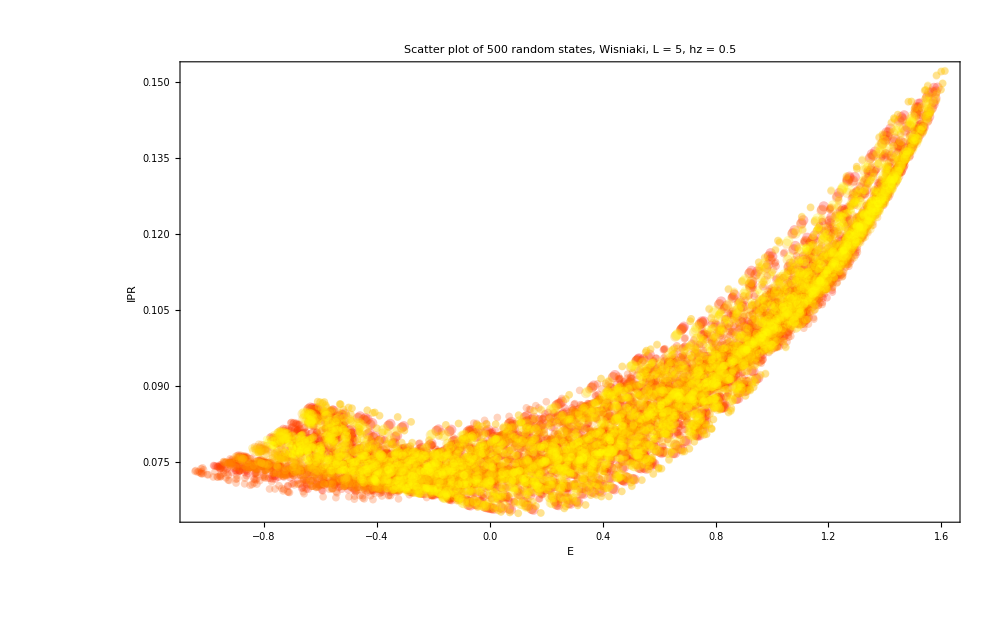

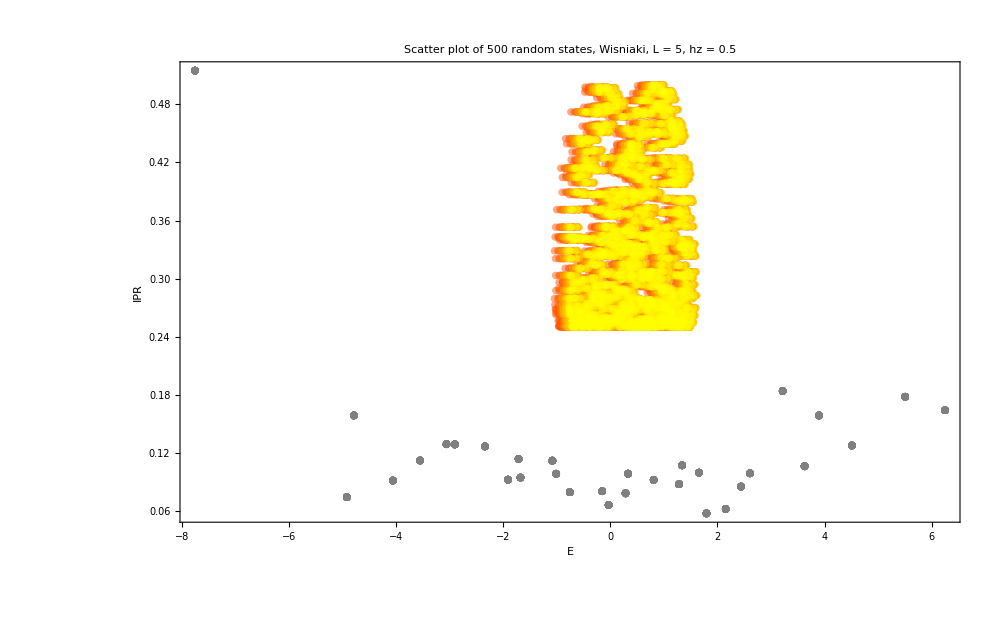

```mathematica
tres=Show[scatterplots,PlotRange->All]
cuatro=Show[scatterplots2c,PlotRange->All]
```

```mathematica
energyentropy=Table[Tr[(MatrixPartialTrace[Dyad[i],2,{2,2^(L-1)}])^2],{i,eigenvec}];
ListPlot[Transpose[{eigenval,energyentropy}],PlotRange->All];
```

```mathematica
a=ListPlot[{Transpose[{eigenval,energyentropy}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",35,Black],PlotStyle->{Directive[Brown,Opacity[0.5]],Directive[Gray,Opacity[1]]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],HoldForm[TraditionalForm[IPR]]},ImageSize->1000];
Show[{scatterplots2c,a},PlotRange->All];
```

## Quantum channel

```mathematica
tf=10.;
dt=0.1;
(*QUANTUM CHANNEL*)
ψe=ψec;
styles={Style["Random product state, L = "<>ToString[L]<>", hz = "<>ToString[hz],40,Black]};

(*For each initial state compute bloch sphere dynamics and export it as video*)
allchoieigenvalues={};
allchoipurities={};
spectrum={};
allchoeigenvec={};

Do[

choiEigenvalues={};
choiEigenvectors={};
choipurities={};

Do[
superOp=Superoperator[t,ψe[[i]],eigenval,eigenvec,L];
AppendTo[spectrum,Eigenvalues[superOp]];
AppendTo[choiEigenvalues,Transpose[{ConstantArray[t,4],Eigenvalues[1/2.Reshuffle[superOp]]}]];
AppendTo[choiEigenvectors,Transpose[Sort[Transpose[Eigensystem[1/2.Reshuffle[superOp]]]]][[2]]];
AppendTo[choipurities,Transpose[{t,Purity[1/2.Reshuffle[superOp]]}]];
,{t,0,tf,dt}];

AppendTo[allchoieigenvalues,Chop[choiEigenvalues]];
AppendTo[allchoeigenvec,Chop[choiEigenvectors]];
AppendTo[allchoipurities,Chop[choipurities]];
,{i,Length[ψe]}];
```

```mathematica
limit=Plot[{0.5,0.25},{x,0,tf},PlotStyle->Directive[RGBColor[0.93,0.07,0.66],Dashed]];
enerpury=Plot[{energyentropy},{x,0,tf},PlotStyle->Directive[Brown,Opacity[0.05]]];
listplots={};
puritiesplots={};

Do[

AppendTo[listplots,
Show[{
ListPlot[Transpose[Chop[allchoieigenvalues[[i]]]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[coloursc[[i]],Opacity[0.15]],
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{"StyleBox[\"t\",FontSlant->\"Italic\"]","λ(Choi)"},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->1000]
,limit}]];

AppendTo[puritiesplots,
Show[{
ListPlot[Chop[allchoipurities[[i]]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[coloursc[[i]],Opacity[0.5]],
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{HoldForm[TraditionalForm[t]],HoldForm[TraditionalForm[Tr[𝒟^2]]]},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->1000]
,limit}]];

,{i,Length[ψe]}];
```

```mathematica
plotmeanchoieigenval=ListPlot[Transpose[Chop[Mean[allchoieigenvalues]]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Thick],
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{"StyleBox[\"t\",FontSlant->\"Italic\"]","λ(Choi)"},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->1000];

plotmeanchoipurity=ListPlot[Chop[Mean[allchoipurities]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Black,Thick],
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{HoldForm[TraditionalForm[t]],HoldForm[TraditionalForm[Tr[𝒟^2]]]},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->1000];
```

```mathematica
testimage=Grid[{{Show[{listplots,plotmeanchoieigenval}],Show[scatterplots2c,PlotRange->All]},{Show[{puritiesplots,plotmeanchoipurity},PlotRange->{{0,tf},All}],Show[{spectrumplots[[1]],spectrumplots[[16]],spectrumplots[[-1]]}]}},Spacings->{5,5},Alignment->{Center,Center},Frame->All];
Export["frame_wisniacki_L_"<>ToString[L]<>"_hz_"<>ToString[hz]<>"_hx_"<>ToString[hx]<>"_J_"<>ToString[J]<>"_excitation_randomrealmiddle_fourth_"<>ToString[ale2]<>"_tf_"<>ToString[tf]<>".png",testimage];
```

## spectrum

```mathematica
tlist=Range[0,tf,dt];
newspectrum=ArrayReshape[spectrum,{ale2,Length[tlist],4}];
spectrumplots=Table[ComplexListPlot[newspectrum[[i]],PlotRange->{{-1.02,1.02},{-1.02,1.02}},PlotStyle->coloursc[[i]],PlotLabel->Style["Spectrum plot of Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>", tf = "<>ToString[tf],35,Black],ImageSize->1000,PlotTheme->"Detailed",GridLines->None,Frame->True,Axes->True],{i,Length[newspectrum]}];
```

```mathematica
Table[Export["spectrum_blochtest_parityenvironment_fourths_L_"<>ToString[L]<>"_hz_"<>ToString[hz]<>"_hx_"<>ToString[hx]<>"_tf_"<>ToString[tf]<>"_enviroment_end_"<>ToString[i]<>".png",spectrumplots[[i]]],{i,ale2}]
```

```mathematica
Export["spectrum_L_"<>ToString[L]<>"_hz_"<>ToString[hz]<>"_tf_"<>ToString[tf]<>".mp4",spectrumplots,"FrameRate"->1]
```

$Aborted

```mathematica
tlist=Range[0,tf,dt];
newspectrum=spectrum[[1;;Length[tlist]]];
```

```mathematica
spectrumplots3=Table[ComplexListPlot[newspectrum[[;;i]],PlotRange->{{-1.02,1.02},{-1.02,1.02}},PlotStyle->Table[Blend[{LightRed,Red},j/(1.5*i)],{j,i}],PlotLabel->Style["Spectrum plot of Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>", tf = "<>ToString[tf]<>", t ="<>ToString[tlist[[i]]],25,Black],ImageSize->600,PlotTheme->"Detailed",GridLines->None,Frame->True,Axes->True],{i,Length[tlist]}];
```

```mathematica
ListAnimate[spectrumplots3,AnimationRunning->False]
```

```mathematica
Export["spectrum_blochtest_L_"<>ToString[L]<>"_hz_"<>ToString[hz]<>"_tf_"<>ToString[tf]<>".mp4",spectrumplots3,"FrameRate"->5]
```

spectrum_blochtest_L_5_hz_0.5_tf_5.mp4

## example

```mathematica
(*Example Trajectory*)trajectory=Table[{Cos[t],Sin[t]},{t,0,2 Pi,0.1}];

(*Generate frames with fading effect and highlighted current position*)
frames=Table[Show[ListPlot[trajectory[[;;i]],PlotStyle->Table[Blend[{Red,LightRed},j/i],{j,i}],Axes->True,PlotRange->{{-1.5,1.5},{-1.5,1.5}}],Graphics[{PointSize[Large],Red,Point[trajectory[[i]]]}]],{i,Length[trajectory]}];

(*Create an animation*)
ListAnimate[frames,AnimationRunning->False]
```

## Different size spectrums

```mathematica
spectrumplots=Table[Grid[{{spectrumplots3[[i]],spectrumplots4[[i]]},{spectrumplots5[[i]],spectrumplots6[[i]]}},Spacings->{5,5},Alignment->{Center,Center},Frame->All],{i,Length[tlist]}];
```

```mathematica
Table[Export["spectrum_L_3456_"<>ToString[L]<>"_hz_"<>ToString[hz]<>"_"<>ToString[i]<>".png",spectrumplots[[i]]],{i,Length[spectrumplots]}]
```

```mathematica
Export["spectrum_L_3456_"<>ToString[L]<>"_hz_"<>ToString[hz]<>".mp4",spectrumplots,"FrameRate"->10]
```

Export::interr2: An unknown internal error occurred. Consult Internal`$LastInternalFailure for potential information.

$Failed

## Plotting as a function of t

```mathematica
tlist=Range[0,tf,dt];
newspectrum=spectrum[[1;;Length[tlist]]];
```

```mathematica
spectrumplots=Table[ComplexListPlot[newspectrum[[1;;i]],PlotRange->{{-1.02,1.02},{-1.02,1.02}},PlotStyle->coloursc[[1]],PlotLabel->Style["Spectrum plot of Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>", tf = "<>ToString[tf],35,Black],ImageSize->1000,PlotTheme->"Detailed",GridLines->None,Frame->True,Axes->True],{i,100}];
```

```mathematica
spectrumplots=Table[Grid[{{Show[{listplots,plotmeanchoieigenval}],Show[scatterplots2c,PlotRange->All]},{Show[{puritiesplots,plotmeanchoipurity},PlotRange->{{0,tf},All}],ComplexListPlot[newspectrum[[1;;i]],PlotRange->{{-1.02,1.02},{-1.02,1.02}},PlotStyle->coloursc[[1]],PlotLabel->Style["Spectrum plot of Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>", tf = "<>ToString[tf],35,Black],ImageSize->1000,PlotTheme->"Detailed",GridLines->None,Frame->True,Axes->True]}},Spacings->{5,5},Alignment->{Center,Center},Frame->All],{i,Length[tlist]}];
```

```mathematica
Export["spectrum_L_"<>ToString[L]<>"_hz_"<>ToString[hz]<>".mp4",spectrumplots,"FrameRate"->10]
```

spectrum_L_5_hz_0.5.mp4

```mathematica
ListAnimate[spectrumplots,AnimationRunning->False]
```

## Kraus

```mathematica
tlist//Length
```

101

```mathematica
allchoeigenvec//Dimensions
```

{30,101,4,4}

```mathematica
allchoeigenvec[[1,1]]//Dimensions
```

{4,4}

```mathematica
allchoieigenvalues[[1,2]]
```

{{0.05,0.999994},{0.05,6.22491×10^-6},{0.05,0},{0.05,0}}

```mathematica
Table[MatrixForm[ArrayReshape[i,{2,2}]],{i,allchoeigenvec[[1,2]]}]
```

{(0.0352551-0.00103562 ⅈ | 0.0414221+0.70141 ⅈ
-0.0207987+0.709493 ⅈ | 0.0353896),(-0.0117535+0.00255156 ⅈ | -0.102054-0.703211 ⅈ
0.0393569+0.702318 ⅈ | 0.0116449),(-0.706133-0.0351598 ⅈ | -0.0012712+0.0117598 ⅈ
-0.00048877-0.0117948 ⅈ | 0.707008),(0.705345+0.0352087 ⅈ | 0.000879667-0.0353261 ⅈ
0.000882603-0.035326 ⅈ | 0.706223)}

## SP(t)

```mathematica
ψec//Dimensions
```

{10,64}

```mathematica
newψec=Table[Flatten[KroneckerProduct[haar[1],i]],{i,ψec}];
```

```mathematica
tlist=Range[0,tf,0.1];
ψct=Table[StateEvolution[t,j,eigenval,eigenvec],{j,newψec},{t,0,tf,0.1}];
```

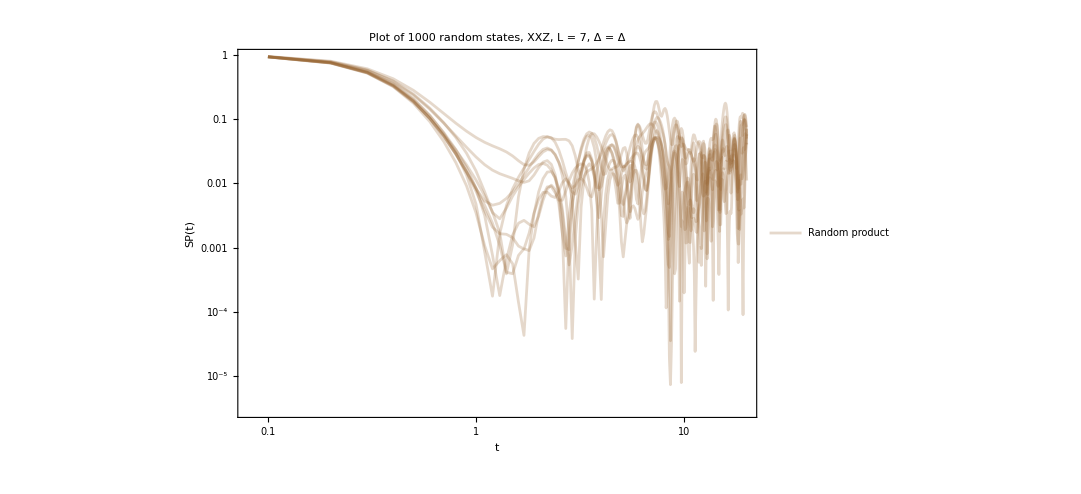

```mathematica
singlec=ListLogLogPlot[Table[{tlist[[i]],Abs[Conjugate[ψct[[j,1]]].ψct[[j,i]]]^2},{j,Length[ψct]},{i,Length[Range[0,tf,0.1]]}],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Plot of "<>ToString[ale]<>" random states, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->{Directive[Brown,Opacity[0.25]]},PlotRange->All,ImageSize->800,PlotLegends->{Style["Random product",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["SP(t)"]}]
```

# Fixed point

```mathematica
L=5;
hx=1;
J=1;
hz=0.5;
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

```mathematica
ale2=10;
blochtest=Table[qubit[i,0],{i,0,Pi,Pi/ale2}];
coloursc=Table[RGBColor[i,i/ale2,1-i],{i,ale2+1}];
```

```mathematica
(*QUANTUM CHANNEL*)
ψe=Table[Flatten[KroneckerProduct[coherentstate[qubit[0,0],L-2],i]],{i,blochtest}];
```

```mathematica
Clear[evol];
evol[n_]:=(1/(n+1))Total[Table[MatrixPower[superop,n].ini,{i,0,n}]]
```

```mathematica
nlist=Range[0,100];
```

```mathematica
plots={};
Do[

tf=1;
ini=ArrayFlatten[Dyad[haar[1]],1];
superop=Superoperator[tf,ψe[[j]],eigenval,eigenvec,L];
states=Table[evol[n],{n,nlist}];
spectrums=Table[Sort[Eigenvalues[rho[i]]],{i,states}];
plot=ListPlot[Flatten[Table[Transpose[{ConstantArray[nlist[[i]],2],Chop[spectrums[[i]]]}],{i,Length[nlist]}],1],PlotStyle->coloursc[[j]],PlotTheme->"Detailed",ImageSize->600,PlotRange->All];
AppendTo[plots,plot];
,{j,Length[ψe]}]
```

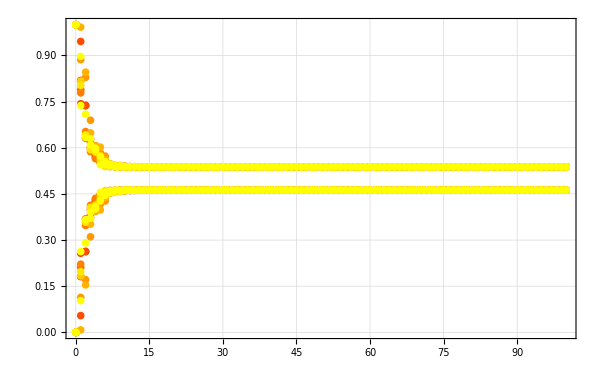

```mathematica
Show[plots]
```

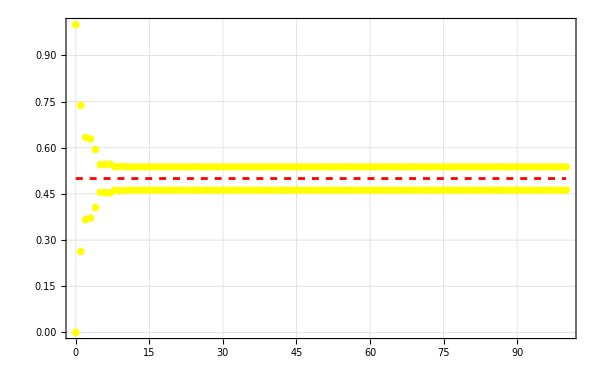

-Graphics3D-

```mathematica
plot2=ListPointPlot3D[Table[Chop[bloch[rho[i]]],{i,states}],PlotRange->All,BoxRatios->{1, 1, 1}];
origin=ListPointPlot3D[{{0,0,0}},PlotStyle->Directive[Black,PointSize[0.03]]];
mixed=Plot[0.5,{x,0,nlist[[-1]]},PlotStyle->Directive[Red,Dashed],PlotRange->All];
Show[{plot,mixed}]
Show[{plot2,plotsphere2,origin}]
```

```mathematica
points=Table[Chop[bloch[rho[i]]],{i,states}];
frames=Table[ListPointPlot3D[points[[1;;i]],PlotRange->{{-1,1},{-1,1},{-1,1}},BoxRatios->{1, 1, 1}],{i,Length[points]}];
```

```mathematica
ListAnimate[frames,AnimationRunning->False]
```

# Random Kraus

```mathematica
(*Parameters*)
(*Dimension for a qubit*)
dim=2; 
Clear[randomKraus];
randomKraus[rank_]:=Module[{a=Table[RandomComplex[{-1-I,1+I},{dim,dim}],{i,rank}],b,c},
b=Total[ConjugateTranspose[#].#&/@a];
c=Table[a[[i]].Inverse[MatrixPower[b,1/2]],{i,rank}]
];
Clear[choi];
choi[kraus_]:=Module[{a},
a=(1/2)Sum[Dyad[Flatten[ArrayReshape[i,{1,4}]]],{i,kraus}]
];
Clear[EEntropy];
EEntropy[choi_]:=1-Tr[Chop[choi.choi]];
```

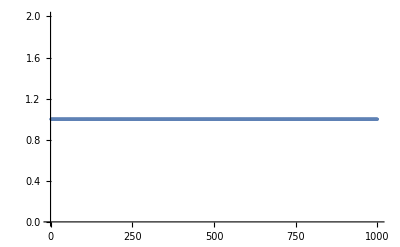

```mathematica
kraustest=Table[randomKraus[5],{i,1000}];
verifications=Table[Total[ConjugateTranspose[#].#&/@i],{i,kraustest}];
Table[If[Chop[i]==IdentityMatrix[dim],1,0] ,{i,verifications}]//ListPlot
```

```mathematica
chois=Table[choi[i],{i,kraustest}];
entropies=Table[EEntropy[i],{i,chois}];
```

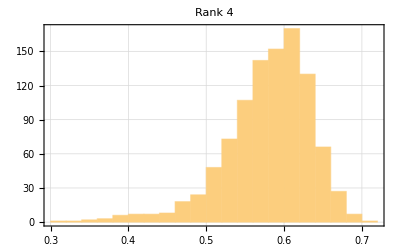

```mathematica
Histogram[entropies,20,PlotTheme->"Detailed",PlotRange->All,PlotLabel->Style["Rank 4",25,Black]]
```

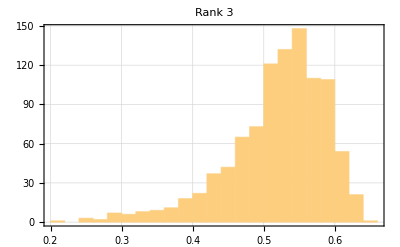

```mathematica
Histogram[entropies,20,PlotTheme->"Detailed",PlotRange->All,PlotLabel->Style["Rank 3",25,Black]]
```

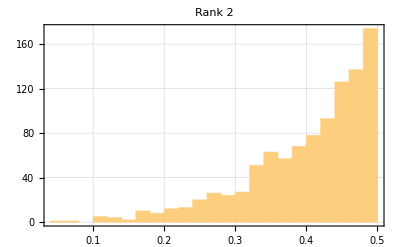

```mathematica
Histogram[entropies,20,PlotTheme->"Detailed",PlotRange->All,PlotLabel->Style["Rank 2",25,Black]]
```

## Ising

```mathematica
L=6;
hx=1;
J=1;
tlist=Range[0,50,0.1];
```

```mathematica
hz=3.;
Clear[H,eigenval,eigenvec,superOp];
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
ψe=RandomChainProductState[L-1];
superOp=ParallelTable[Superoperator[t,ψe,eigenval,eigenvec,L],{t,tlist}];
choisising=Table[(1/2)Reshuffle[i],{i,superOp}];
entropiesising=Table[EEntropy[i],{i,choisising}];
```

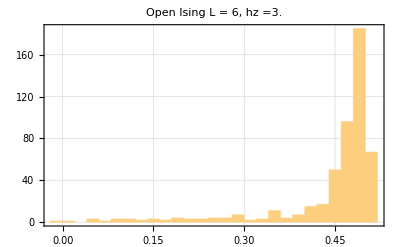

```mathematica
plotb=Histogram[entropiesising,20,PlotTheme->"Detailed",PlotRange->All,PlotLabel->Style["Open Ising L = "<>ToString[L]<>", hz ="<>ToString[hz],25,Black]]
```

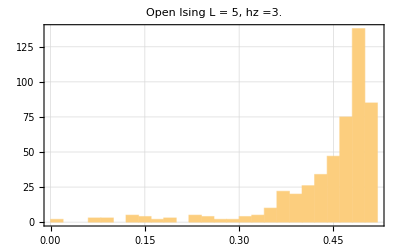

```mathematica
plotb=Histogram[entropiesising,20,PlotTheme->"Detailed",PlotRange->All,PlotLabel->Style["Open Ising L = "<>ToString[L]<>", hz ="<>ToString[hz],25,Black]]
```

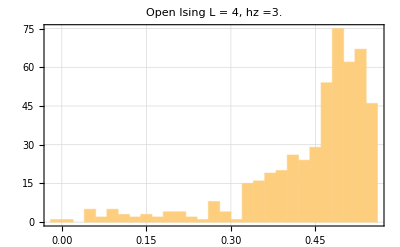

```mathematica
plotb=Histogram[entropiesising,20,PlotTheme->"Detailed",PlotRange->All,PlotLabel->Style["Open Ising L = "<>ToString[L]<>", hz ="<>ToString[hz],25,Black]]
```

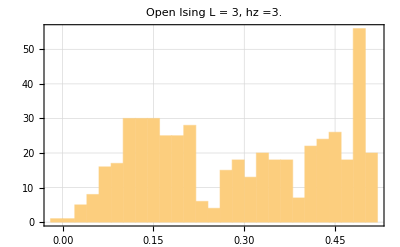

```mathematica
plotb=Histogram[entropiesising,20,PlotTheme->"Detailed",PlotRange->All,PlotLabel->Style["Open Ising L = "<>ToString[L]<>", hz ="<>ToString[hz],25,Black]]
```

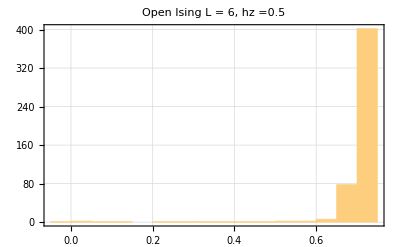

```mathematica
plotb=Histogram[entropiesising,20,PlotTheme->"Detailed",PlotRange->All,PlotLabel->Style["Open Ising L = "<>ToString[L]<>", hz ="<>ToString[hz],25,Black]]
```

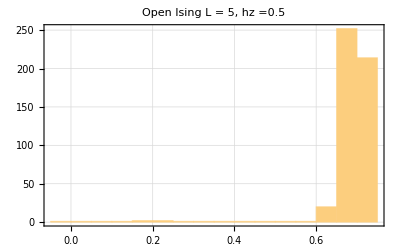

```mathematica
plotb=Histogram[entropiesising,20,PlotTheme->"Detailed",PlotRange->All,PlotLabel->Style["Open Ising L = "<>ToString[L]<>", hz ="<>ToString[hz],25,Black]]
```

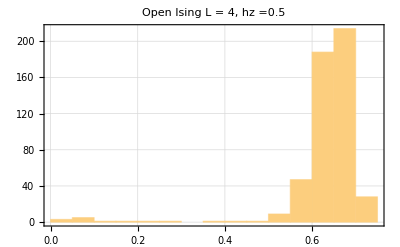

```mathematica
plotb=Histogram[entropiesising,20,PlotTheme->"Detailed",PlotRange->All,PlotLabel->Style["Open Ising L = "<>ToString[L]<>", hz ="<>ToString[hz],25,Black]]
```

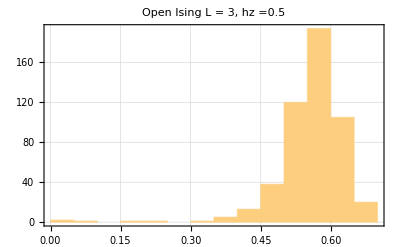

```mathematica
plota=Histogram[entropiesising,20,PlotTheme->"Detailed",PlotRange->All,PlotLabel->Style["Open Ising L = "<>ToString[L]<>", hz ="<>ToString[hz],25,Black]]
```

## Open XXZ Regular

```mathematica
L=5;
tlist=Range[0,50,0.1];
```

```mathematica
Δ=10.;
Clear[H,eigenval,eigenvec,superOp];
H=OpenXXZHamiltonian[L,Δ,0,0];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
ψe=RandomChainProductState[L-1];
superOp=ParallelTable[Superoperator[t,ψe,eigenval,eigenvec,L],{t,tlist}];
choisising=Table[(1/2)Reshuffle[i],{i,superOp}];
entropiesising=Table[EEntropy[i],{i,choisising}];
```

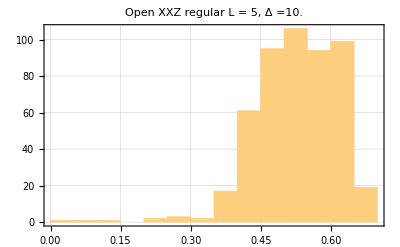

```mathematica
Histogram[entropiesising,20,PlotTheme->"Detailed",PlotRange->All,PlotLabel->Style["Open XXZ regular L = "<>ToString[L]<>", Δ ="<>ToString[Δ],25,Black]]
```

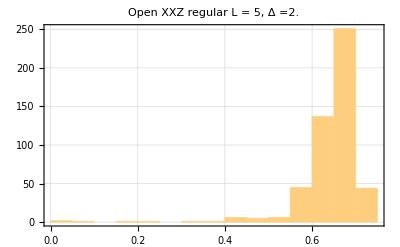

```mathematica
Histogram[entropiesising,20,PlotTheme->"Detailed",PlotRange->All,PlotLabel->Style["Open XXZ regular L = "<>ToString[L]<>", Δ ="<>ToString[Δ],25,Black]]
```

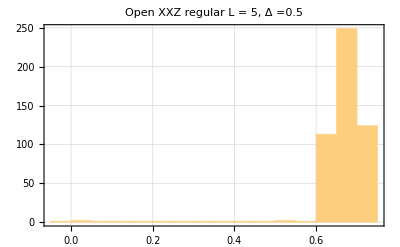

```mathematica
Histogram[entropiesising,20,PlotTheme->"Detailed",PlotRange->All,PlotLabel->Style["Open XXZ regular L = "<>ToString[L]<>", Δ ="<>ToString[Δ],25,Black]]
```

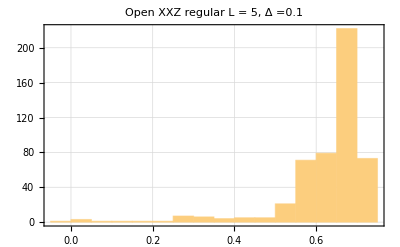

```mathematica
Histogram[entropiesising,20,PlotTheme->"Detailed",PlotRange->All,PlotLabel->Style["Open XXZ regular L = "<>ToString[L]<>", Δ ="<>ToString[Δ],25,Black]]
```

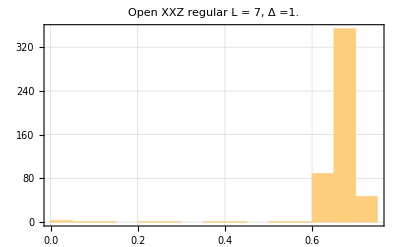

```mathematica
Histogram[entropiesising,20,PlotTheme->"Detailed",PlotRange->All,PlotLabel->Style["Open XXZ regular L = "<>ToString[L]<>", Δ ="<>ToString[Δ],25,Black]]
```

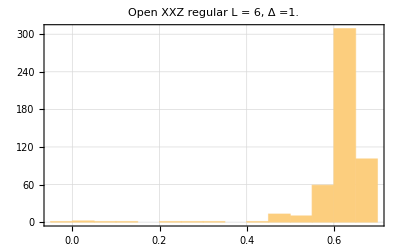

```mathematica
Histogram[entropiesising,20,PlotTheme->"Detailed",PlotRange->All,PlotLabel->Style["Open XXZ regular L = "<>ToString[L]<>", Δ ="<>ToString[Δ],25,Black]]
```

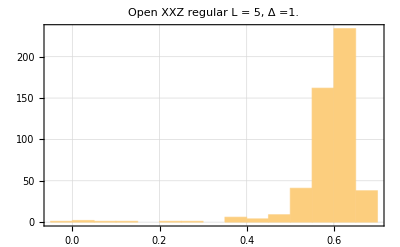

```mathematica
Histogram[entropiesising,20,PlotTheme->"Detailed",PlotRange->All,PlotLabel->Style["Open XXZ regular L = "<>ToString[L]<>", Δ ="<>ToString[Δ],25,Black]]
```

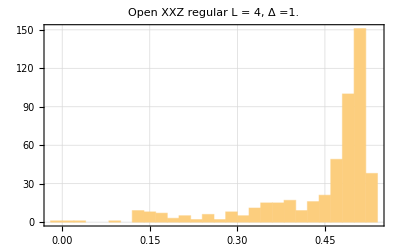

```mathematica
Histogram[entropiesising,20,PlotTheme->"Detailed",PlotRange->All,PlotLabel->Style["Open XXZ regular L = "<>ToString[L]<>", Δ ="<>ToString[Δ],25,Black]]
```

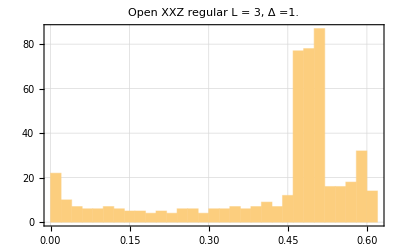

```mathematica
Histogram[entropiesising,20,PlotTheme->"Detailed",PlotRange->All,PlotLabel->Style["Open XXZ regular L = "<>ToString[L]<>", Δ ="<>ToString[Δ],25,Black]]
```

## Ginibre ensembles

```mathematica
(*Parameters*)
dim=2; (*Qubit dimension*)
nKraus=3; (*Number of Kraus operators*)
(*Real Ginibre Ensemble*)
realGinibreKraus=Table[RandomVariate[NormalDistribution[],{dim,dim}],{i,nKraus}];
(*Complex Ginibre Ensemble*)
complexGinibreKraus=Table[RandomComplex[{-1-I,1+I},{dim,dim}],{i,nKraus}];
```

```mathematica
realGinibreKraus//Dimensions
complexGinibreKraus//Dimensions
```

{3,2,2}

{3,2,2}

```mathematica
(*Compute completeness matrix for normalization*)
completenessMatrix=Total[ConjugateTranspose[#].#&/@realGinibreKraus];
(*Rescale Kraus operators*)
normalizedKraus=Table[realGinibreKraus[[i]].Inverse[MatrixPower[completenessMatrix,1/2]],{i,nKraus}];
```

```mathematica
(*Verify completeness condition*)
verification=Total[ConjugateTranspose[#].#&/@normalizedKraus];
Chop[verification]==IdentityMatrix[dim] (*Should return True*)
```

True

## Real Ginibre

```mathematica
Clear[realginibre];
realginibre[rank_,dim_]:=Module[{a=Table[RandomVariate[NormalDistribution[],{dim,dim}],{i,rank}],b,c},
b=Total[ConjugateTranspose[#].#&/@a];
c=Table[a[[i]].Inverse[MatrixPower[b,1/2]],{i,rank}]
];
```

```mathematica
dim=2;
rank=4;
Clear[kraustest];
kraustest=Table[realginibre[2,dim],{i,1000}];
verifications=Table[Total[ConjugateTranspose[#].#&/@i],{i,kraustest}];
newkraus={};
Do[
If[Chop[verifications[[i]]]==IdentityMatrix[dim],AppendTo[newkraus,kraustest[[i]]]];
,{i,Length[kraustest]}];
Length[newkraus]
```

999

```mathematica
chois=Table[choi[i],{i,newkraus}];
entropies=Table[EEntropy[i],{i,chois}];
```

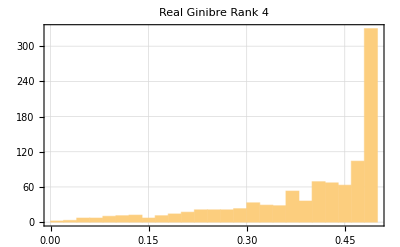

```mathematica
Histogram[entropies,20,PlotTheme->"Detailed",PlotRange->All,PlotLabel->Style["Real Ginibre Rank 4",25,Black]]
```

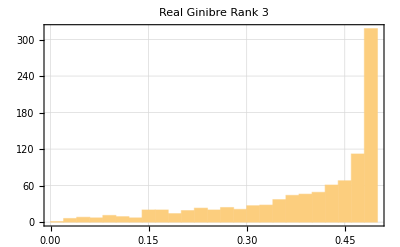

```mathematica
Histogram[entropies,20,PlotTheme->"Detailed",PlotRange->All,PlotLabel->Style["Real Ginibre Rank 3",25,Black]]
```

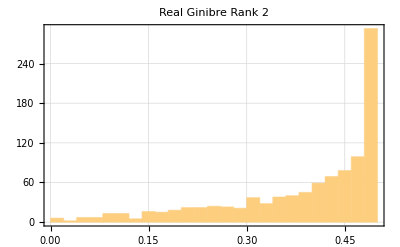

```mathematica
Histogram[entropies,20,PlotTheme->"Detailed",PlotRange->All,PlotLabel->Style["Real Ginibre Rank 2",25,Black]]
```

## Complex Ginibre

Same code as random Kraus, where complex entries are assumed

## Poisson 2D

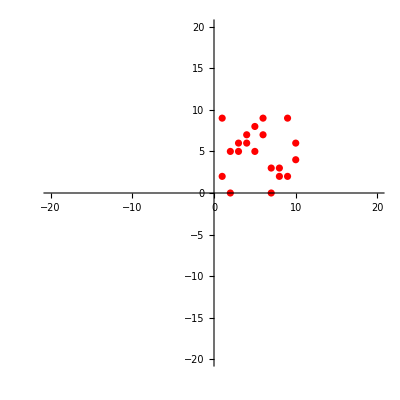

```mathematica
(*Define parameters for the Poisson distribution*)
lambda=5;  (*mean of the Poisson distribution*)

(*Generate a random complex number with independent Poisson-distributed parts*)
complexPoisson=RandomInteger[{0,10},2]+I RandomInteger[{0,10},2];  (*Using integer Poisson approximation*)

(*Plot a set of points in the complex plane*)
points=Table[RandomInteger[{0,10}]+I RandomInteger[{0,10}],{10}];

ListPlot[{Re[points],Im[points]},PlotStyle->Red,PlotRange->{{-20,20},{-20,20}},AspectRatio->1]
```

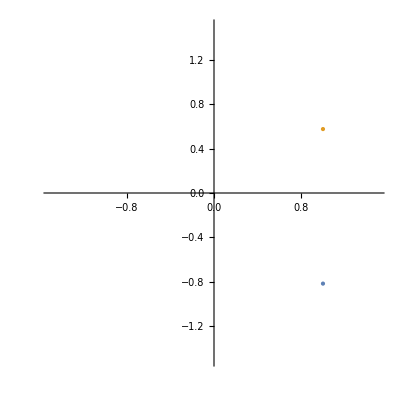

```mathematica
(*Generate n random complex numbers on the unit circle*)n=100;  (*Number of points*)
points=Table[Exp[I RandomReal[{0,2 Pi}]],{n}];

(*Plot the points on the complex plane*)
ListPlot[{Re[points],Im[points]},PlotStyle->PointSize[Medium],PlotRange->{{-1.5,1.5},{-1.5,1.5}},AspectRatio->1]
```